# Reunión del 22-08-2024

## Importando cosas

```mathematica
Get[NotebookDirectory[]<>"DTQW.wl"]
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
<<MaTeX`
```

## Definiendo variables

```mathematica
IndigoC=RGBColor["#729cfc"];
AquaC=RGBColor["#4bd7e5"];
DeepBlueC=RGBColor["#1e2c88"];
```

```mathematica
qlabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"../Mariana/Labels_pos.pdf","../Mariana/Labels_prob.pdf"};
clabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"../Mariana/Labels_pos.pdf","../Mariana/Labels_probc.pdf"};
plotargs={
BaseStyle->{FontFamily->"LM Roman 12",FontSize->15},
Axes->False,
Frame->True,
Mesh->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,Opacity[0.5]]
};
```

```mathematica
TeXLabel[tlist_List]:=MaTeX[
"\\begin{gathered}\n"<>Fold[
StringJoin[#1,"\\\\\n",#2]&,ToString@StringForm["\\text{``}",#]&/@tlist
]<>"\n\\end{gathered}",
FontSize->14,
Magnification->1.3,
"Preamble"->{"\\usepackage{physics}"}
]
```

```mathematica
rowQW[state_,steps_]:=Module[
{rho,prob},
rho=#.#†&@DTQW2[state,steps];
prob=Abs@Diagonal@MatrixPartialTrace[rho,1,{2,201}]
]
QPascal[state_,steps_]:=Module[
{},
TableForm[#,
TableHeadings->{Range[0,steps],Ket[{#}]&/@ Range[-steps,steps]},
TableSpacing->{2, 2},
TableAlignments->Center,
Label
]&@
(rowQW[state,#][[101-steps;;101+steps]]&/@Range[0,steps])
]
```

## Inicializaciones

```mathematica
InitializeDTQW[2,201]
MakeCoin[1/2,0,0];
MakeShift[];
MakeUnitary[];
```

## Resultados

### Triángulos de Pascal cuánticos

Hice un par de funciones para sacar las tablas y obtuvimos

```mathematica
Labeled[
ToBoxes[t1=QPascal[VectorState[{{1,0,0}}],6]]/.(x:GridBox[___]):>MapAt["t \\ p"&,x,{1,1,1}]//RawBoxes,
"ψ_0=0,0",Top,
LabelStyle->Directive[FontSize->18],
Spacings->{0,2}
]
```

t \ p | -6 | -5 | -4 | -3 | -2 | -1 | 0 | 1 | 2 | 3 | 4 | 5 | 6
0 | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0.5 | 0. | 0.25 | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0.125 | 0. | 0.125 | 0. | 0.625 | 0. | 0.125 | 0. | 0. | 0.
4 | 0. | 0. | 0.0625 | 0. | 0.125 | 0. | 0.125 | 0. | 0.625 | 0. | 0.0625 | 0. | 0.
5 | 0. | 0.03125 | 0. | 0.15625 | 0. | 0.125 | 0. | 0.125 | 0. | 0.53125 | 0. | 0.03125 | 0.
6 | 0.015625 | 0. | 0.15625 | 0. | 0.078125 | 0. | 0.125 | 0. | 0.203125 | 0. | 0.40625 | 0. | 0.015625ψ_0=0,0

```mathematica
Labeled[
ToBoxes[t2=QPascal[VectorState[{{1,1,0}}],6]]/.(x:GridBox[___]):>MapAt["t \\ p"&,x,{1,1,1}]//RawBoxes,
"ψ_0=1,0",Top,
LabelStyle->Directive[FontSize->18],
Spacings->{0,2}
]
```

t \ p | -6 | -5 | -4 | -3 | -2 | -1 | 0 | 1 | 2 | 3 | 4 | 5 | 6
0 | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0.5 | 0. | 0.25 | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0.125 | 0. | 0.625 | 0. | 0.125 | 0. | 0.125 | 0. | 0. | 0.
4 | 0. | 0. | 0.0625 | 0. | 0.625 | 0. | 0.125 | 0. | 0.125 | 0. | 0.0625 | 0. | 0.
5 | 0. | 0.03125 | 0. | 0.53125 | 0. | 0.125 | 0. | 0.125 | 0. | 0.15625 | 0. | 0.03125 | 0.
6 | 0.015625 | 0. | 0.40625 | 0. | 0.203125 | 0. | 0.125 | 0. | 0.078125 | 0. | 0.15625 | 0. | 0.015625ψ_0=1,0

```mathematica
Labeled[
ToBoxes[t3=QPascal[VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}],6]]/.(x:GridBox[___]):>MapAt["t \\ p"&,x,{1,1,1}]//RawBoxes,
"ψ_0=+_y,0",Top,
LabelStyle->Directive[FontSize->18],
Spacings->{0,2}
]
```

t \ p | -6 | -5 | -4 | -3 | -2 | -1 | 0 | 1 | 2 | 3 | 4 | 5 | 6
0 | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0.5 | 0. | 0.25 | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0.125 | 0. | 0.375 | 0. | 0.375 | 0. | 0.125 | 0. | 0. | 0.
4 | 0. | 0. | 0.0625 | 0. | 0.375 | 0. | 0.125 | 0. | 0.375 | 0. | 0.0625 | 0. | 0.
5 | 0. | 0.03125 | 0. | 0.34375 | 0. | 0.125 | 0. | 0.125 | 0. | 0.34375 | 0. | 0.03125 | 0.
6 | 0.015625 | 0. | 0.28125 | 0. | 0.140625 | 0. | 0.125 | 0. | 0.140625 | 0. | 0.28125 | 0. | 0.015625ψ_0=+_y,0

### Graficas de las distribuciones de probabilidad

```mathematica
Manipulate[
ListLinePlot[({Range[-6,6],#}ᵀ)[[Mod[i-1,2]+1;;;;2]],
plotargs,
PlotLabel->StringForm["Pasos: `` – Estado inicial: 0,0",i-1],
FrameLabel->qlabels,
PlotStyle->IndigoC,
PlotRange->{{-6,6},{0,1}},
PlotRangePadding->Scaled[.05]
]&@t1[[1,i]],{i,1,7,1}
]
```

```mathematica
Manipulate[
ListLinePlot[({Range[-6,6],#}ᵀ)[[Mod[i-1,2]+1;;;;2]],
plotargs,
PlotLabel->StringForm["Pasos: `` – Estado inicial: 1,0",i-1],
FrameLabel->qlabels,
PlotStyle->IndigoC,
PlotRange->{{-6,6},{0,1}},
PlotRangePadding->Scaled[.05]
]&@t2[[1,i]],{i,1,7,1}
]
```

```mathematica
Manipulate[
ListLinePlot[({Range[-6,6],#}ᵀ)[[Mod[i-1,2]+1;;;;2]],
plotargs,
PlotLabel->StringForm["Pasos: `` – Estado inicial: +_y,0",i-1],
FrameLabel->qlabels,
PlotStyle->IndigoC,
PlotRange->{{-6,6},All},
PlotRangePadding->Scaled[.05]
]&@t3[[1,i]],{i,1,21,1}
]
```

### Grafica del estado entrelazado vs el producto

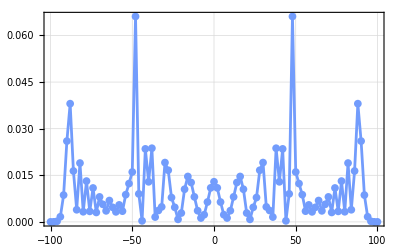

```mathematica
ListLinePlot[{Range[-100,100,2],#[[;;;;2]]}ᵀ,
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100 – Estado producto"}],
FrameLabel->qlabels,
PlotStyle->IndigoC,
PlotRange->All
]&@Module[
{phi,rho,probs},
phi=VectorState[{{1/2,0,20},{ⅈ/2,1,20},{1/2,0,-20},{ⅈ/2,1,-20}}];
rho=#.#†&@DTQW2[phi,100];
probs=Abs@Diagonal@MatrixPartialTrace[rho,1,{2,201}];
probs
]
```

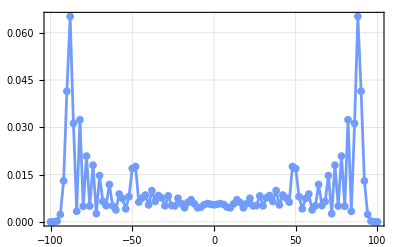

```mathematica
ListLinePlot[{Range[-100,100,2],#[[;;;;2]]}ᵀ,
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100 – Estado Entrelazado"}],
FrameLabel->qlabels,
PlotStyle->IndigoC,
PlotRange->All
]&@Module[
{phi,rho,probs},
phi=VectorState[{{1/Sqrt[2],0,20},{ⅈ/Sqrt[2],1,-20}}];
rho=#.#†&@DTQW2[phi,100];
probs=Abs@Diagonal@MatrixPartialTrace[rho,1,{2,201}];
probs
]
```

```mathematica
" \!\(\*StyleBox[\"p\", \"TI\"]\) "
```

p

```mathematica
"DTQW2wDecoherence[state,p,n] evaluates n steps in the DTQW with initial VectorState state using the Coin and Shift operators created by their respective functions and with p probability of getting a phase–flip."
```